FittedModel[554.618/(1+42.9926 ⅇ^(-0.538518 x))]

0.999619

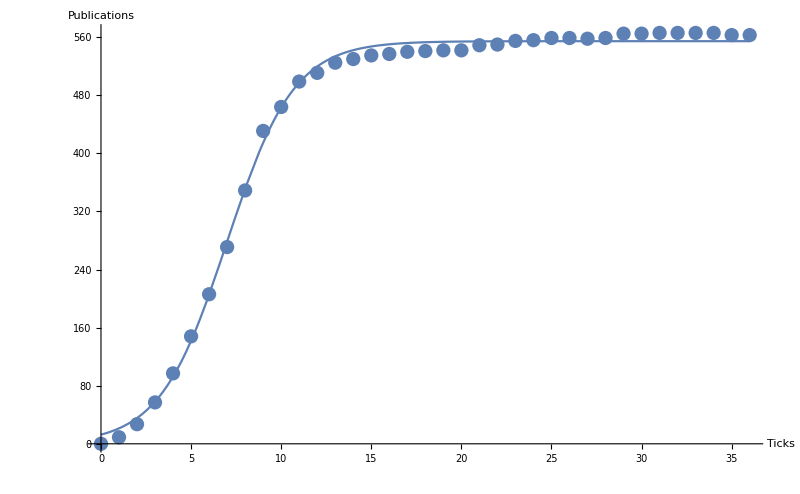

```mathematica
dataPublicationsCurve = Import["/home/fabianact/Tesis/Pruebas/ModelGrid/testTables/publicationstest-curve.csv"];
fitFkt=NonlinearModelFit[dataPublicationsCurve,c/(1+a Exp[-b x]),{a,b,c},x]
fitFkt[{"BestFit","ParameterTable"}];
fitFkt["AdjustedRSquared"]
plot=Show[ListPlot[dataPublicationsCurve,ImageSize->800,AxesLabel->{"Ticks","Publications"}],Plot[fitFkt[x],{x,0,36}]]
Export["fit.png",plot];
```